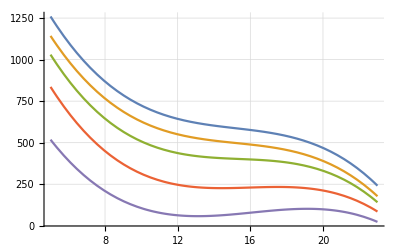

```mathematica
(*   SAM's constants *)
f90[x_]:=1000*(1.61084-0.306923 x+0.0197198 x^2-0.000407671 x^3);
f93[x_]:=1000*(2.16094-0.369614 x+0.0233568 x^2-0.000487402 x^3);
f95[x_]:=1000*(2.3584-0.372112 x+0.0238681 x^2-0.00051654 x^3);
f97[x_]:=1000*(2.41999-0.35643 x+0.0226776 x^2-0.000496512 x^3);
f99[x_]:=1000*(2.58658-0.370335 x+0.023584 x^2-0.000518103 x^3);
Plot[{f99[x],f97[x],f95[x],f93[x],f90[x]},{x,5,23},
GridLines->Automatic,
PlotRange->{{0,23},{0,All}}]
```

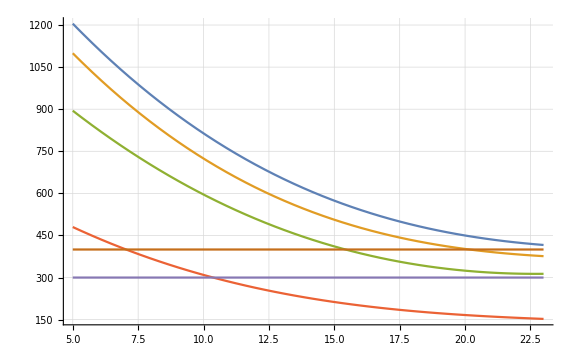

1782.58  -136.573  4.44288  -0.0472998

1675.28  -138.096  4.87514  -0.0576756

1322.79  -99.6022  2.89822  -0.0206909

749.259  -65.2788  2.45103  -0.0322034

```mathematica
(*   Tongtong's constants *)
c093=1782.58;c193=-136.573;c293=4.44288;c393=-0.0472998;
c095=1675.28;c195=-138.096;c295=4.87514;c395=-0.0576756;
c097=1322.79;c197=-99.6022;c297=2.89822;c397=-0.0206909;
c099=749.259;c199=-65.2788;c299=2.45103;c399=-0.0322034;

ff[x_,c0_,c1_,c2_,c3_]:=c0+c1*x+c2*x*x+c3*x*x*x;

Plot[{
ff[x,c093,c193,c293,c393],
ff[x,c095,c195,c295,c395],
ff[x,c097,c197,c297,c397],
ff[x,c099,c199,c299,c399],300,400},
{x,5,23},
GridLines->Automatic,
ImageSize->Large,
PlotRange->{{0,23},{0,All}}]
Print[c093,"  ",c193,"  ",c293,"  ",c393]
Print[c095,"  ",c195,"  ",c295,"  ",c395]
Print[c097,"  ",c197,"  ",c297,"  ",c397]
Print[c099,"  ",c199,"  ",c299,"  ",c399]
```

```mathematica
Print[c093,"  ",c193,"  ",c293,"  ",c393]
Print[c095,"  ",c195,"  ",c295,"  ",c395]
Print[c097,"  ",c197,"  ",c297,"  ",c397]
Print[c099,"  ",c199,"  ",c299,"  ",c399]
```

1782.58  -136.573  4.44288  -0.0472998

1675.28  -138.096  4.87514  -0.0576756

1322.79  -99.6022  2.89822  -0.0206909

749.259  -65.2788  2.45103  -0.0322034

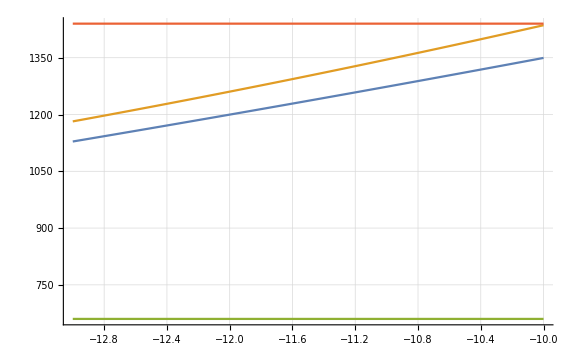

2252.66  103.169  1.2853

2676.83  154.409  3.03128

```mathematica
(*   Moller constants *)
p03s=2252.66;p13s=103.169;p23s=1.2853;
p04s=2676.83;p14s=154.409;p24s=3.03128;


gg[x_,c0_,c1_,c2_]:=c0+c1*x+c2*x*x;

Plot[{
gg[x,p03s,p13s,p23s],
gg[x,p04s,p14s,p24s],660.,1440.},
{x,-13,-10},
GridLines->Automatic,
ImageSize->Large,
PlotRange->{{-13,-10},{0,All}}]
Print[p03s,"  ",p13s,"  ",p23s]
Print[p04s,"  ",p14s,"  ",p24s]
```